```mathematica
u[x_,t_]=1/6(ⅇ^(2x+t)-ⅇ^(2x-5t))+ⅇ^(-3t)(x-t);
D[u[x,t], t]+D[u[x,t], x]+3u[x,t]//FullSimplify
```

ⅇ^(t+2 x)

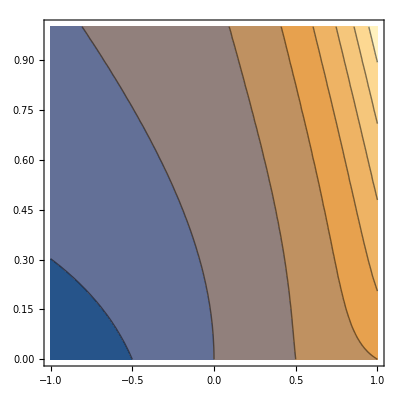

```mathematica
ContourPlot[u[x,t],{x,-1,1},{t,0,1},PlotRange->All]
```

```mathematica
u[x_,t_]=1/(1+(x-1/2 t^2)^2-t)
D[u[x,t], t]+t D[u[x,t], x]-u[x,t]^2//FullSimplify
u[x,0]
Plot3D[u[x,t],{x,-1,1},{t,0,1},PlotRange->All]
```

1/(1-t+(-t^2/2+x)^2)

0

1/(1+x^2)

-Graphics3D-

```mathematica
Solve[D[u[x,t], x]==0,x]//FullSimplify
u[t^2/2,t]
```

{{x→t^2/2}}

1/(1-t)

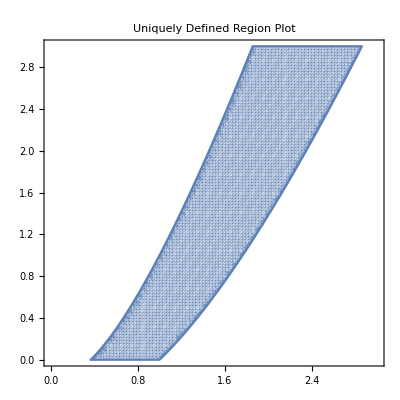

```mathematica
RegionPlot[0<y/x-Log[x]&&y/x-Log[x]<1,{x,0,3},{y,0,3},PlotPoints->100,PlotLabel->"Uniquely Defined Region Plot"]
```

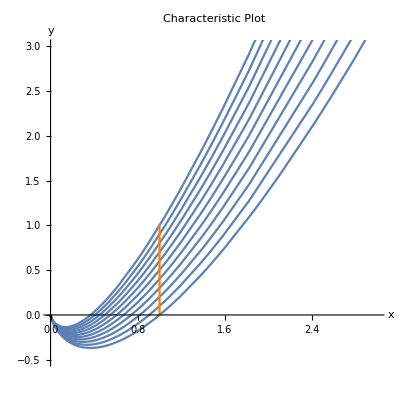

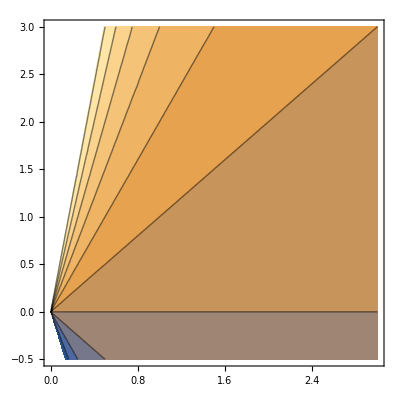

```mathematica
Show[
ParametricPlot[{ⅇ^τ,ⅇ^τ(#+τ)},{τ,-100,2},
PlotRange->{{0,3},{-0.5,3}}]&/@Table[x,{x,0,1,0.1}],
ParametricPlot[{1,s},{s,0,1},PlotStyle->Orange],
PlotLabel->"Characteristic Plot",
AxesLabel->{"x","y"},
AspectRatio->1
]
ContourPlot[y/x,{x,0,3},{y,-0.5,3}]
```

x-y

1+x

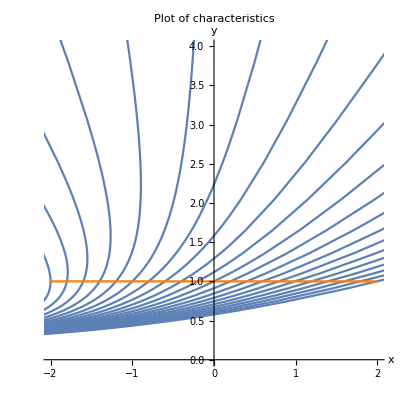

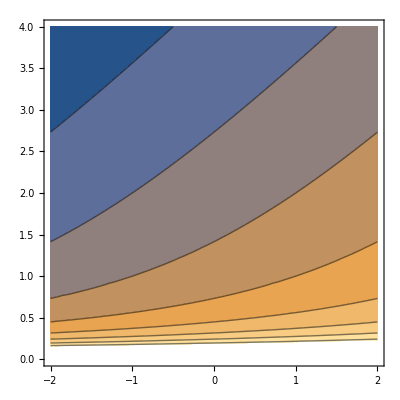

```mathematica
u[x_,y_]=2/y-y+x;
(y+u[x,y])D[u[x,y], x]+y D[u[x,y], y]//FullSimplify
u[x,1]
Show[
ParametricPlot[{ⅇ^τ(1+#)-ⅇ^-τ,ⅇ^τ},{τ,-5,5},PlotRange->{{-2,2},{0,4}}
]&/@Table[s,{s,-2,2,0.2}],
ParametricPlot[{s,1},{s,-2,2},PlotStyle->Orange],
PlotLabel->"Plot of characteristics",
AxesLabel->{"x","y"}]
ContourPlot[u[x,y],{x,-2,2},{y,0,4}]
```

```mathematica
u1[x_,t_]=f[(x-t-x t)/(1+t+x t)]-t-Log[(1-t-(x-t-x t)/(1+t+x t)t)];
u2[x_,t_]=g[(t+t x-x)/(1+x)]-x/(1+x)-Log[1-x/(1+x)];
u[x_,t_]=Piecewise[{{u1[x,t], t<=x/(1+x)}, {u2[x,t], t>x/(1+x)}}];
u1[x,x/(1+x)]//FullSimplify
u2[x,x/(1+x)]//FullSimplify
Evaluate[D[u1[x,t], x]]/.{t->x/(1+x)}//FullSimplify
Evaluate[D[u1[x,t], t]]/.{t->x/(1+x)}//FullSimplify
Evaluate[D[u2[x,t], x]]/.{t->x/(1+x)}//FullSimplify
Evaluate[D[u2[x,t], t]]/.{t->x/(1+x)}//FullSimplify
```

-1+1/(1+x)+f[0]-Log[1/(1+x)]

-1+1/(1+x)+g[0]-Log[1/(1+x)]

(x+f'[0])/(1+x)^2

-f'[0]

(x-g'[0])/(1+x)^2

g'[0]

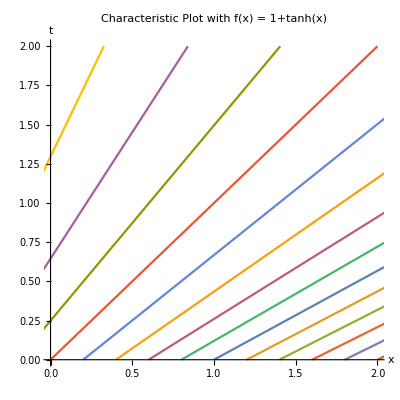

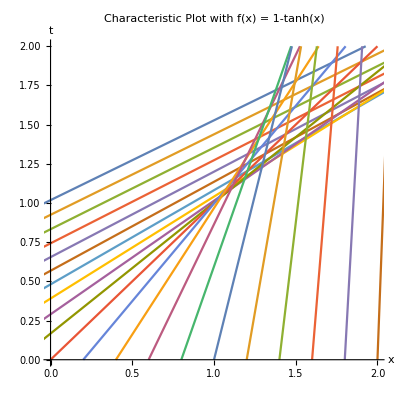

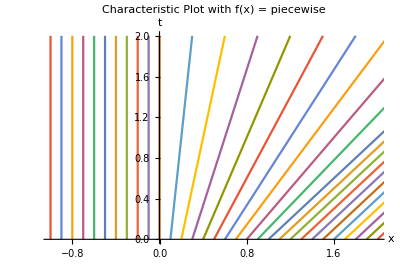

```mathematica
r[s_,τ_,F_]={s+F[s]τ,τ};
f[x_]=1+Tanh[x];
ParametricPlot[Evaluate[r[#,t,f]&/@Table[s,{s,-2,2,0.2}]],{t,0,2},
PlotRange->{{0,2},{0,2}},
PlotLabel->"Characteristic Plot with f(x) = 1+tanh(x)",
AxesLabel->{x,t}]
f[x_]=1-Tanh[x];
ParametricPlot[Evaluate[r[#,t,f]&/@Table[s,{s,-2,2,0.2}]],{t,0,2},PlotRange->{{0,2},{0,2}},
PlotLabel->"Characteristic Plot with f(x) = 1-tanh(x)",
AxesLabel->{x,t}]
f[x_]=Piecewise[{{0, x<0}, {x, 0<=x<1}, {1, 1<=x}}];
ParametricPlot[Evaluate[r[#,t,f]&/@Table[s,{s,-2,2,0.1}]],{t,0,2},PlotRange->{{-1,2},{0,2}},
PlotLabel->"Characteristic Plot with f(x) = piecewise",
AxesLabel->{x,t}]
```

```mathematica
u[x_,t_,a_]=Piecewise[{{Piecewise[{{0, x+t<-a}, {1/2(t+x+a), x-t<-a&&-a<x+t}, {t, -a<x-t&&x+t<a}, {1/2(t-x+a), x-t<a&&a<x+t}, {0, a<x-t}}], 0<=t<a}, {Piecewise[{{0, x+t<-a}, {1/2(t+x+a), -a<x+t&&x+t<a}, {a, x-t<-a&&a<x+t}, {1/2(t-x+a), -a<x-t&&x-t<a}, {0, a<x-t}}], a<=t}}];
ui[x_,t_,a_]:=1/2∫_(x-t)^(x+t) Piecewise[{{1, Abs[y]<a}, {0, True}}]ⅆy;
Animate[{Plot[u[x,t,1],{x,-5,5},PlotRange->{All,{0,1}}],
Plot[ui[x,t,1],{x,-5,5},PlotRange->{All,{0,1}}]},{t,0,5}]
```

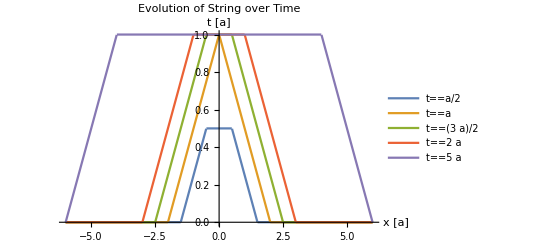

```mathematica
plot=Plot[Evaluate[u[x,#,a]&/@{a/2,a,3a/2,2a,5a}/.a->1],{x,-6,6},PlotRange->{All,{0,1}},
PlotLegends->{t==a/2,t==a,t==3a/2,t==2a,t==5a},
PlotLabel->"Evolution of String over Time",
AxesLabel->{"x [a]","t [a]"}]
Export["/home/merlin/Documents/LaTeX/APPM 5470 PDEs/Assignments/HW02/images/string.png",plot];
```